```mathematica
(* This is a mathematical model for a group making a binary choice. Let i=1,...,N index the choosers. Each has a probability, or preference, function p_i(t) which varies over time. A sigmoid function σ, which may be a disrete step function, is applied to make a binary choice. We then sum the values, and divide by the total. To get a smooth function, we can mollify by using logistic sigmoid with a parameter q. A standard example would be a poll tracker, as FiveThirtyEight has, which measures whether or not a group of individuals approves of the president's performance or not. *)
```

```mathematica
(* define the (smooth) sigmoid function *)
```

```mathematica
σ=Function[{q,y},1/(1+Exp[-q*(y-1/2)])];
```

```mathematica
Manipulate[Plot[σ[q,y],{y,-5,5},PlotRange->{0,1},PlotLabel->"q="<>ToString[q]],{q,0,100,.1}]
```

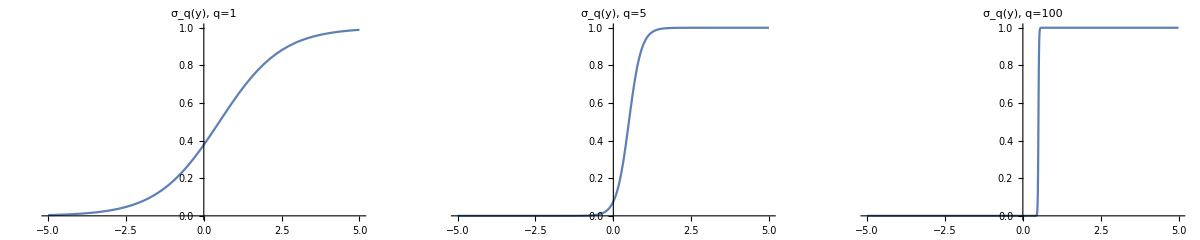

```mathematica
GraphicsRow[{Plot[σ[1,y],{y,-5,5},PlotRange->{0,1},PlotLabel->"σ_q(y), q=1"],Plot[σ[5,y],{y,-5,5},PlotRange->{0,1},PlotLabel->"σ_q(y), q=5"],Plot[σ[100,y],{y,-5,5},PlotRange->{0,1},PlotLabel->"σ_q(y), q=100"]}]
```

```mathematica
(* derivatives of the sigmod function *)
```

{(5 ⅇ^(5/2+5 y))/((ⅇ^(5/2)+ⅇ^(5 y))^2),(25 ⅇ^(5 y) (ⅇ^5-ⅇ^(5/2+5 y)))/((ⅇ^(5/2)+ⅇ^(5 y))^3),(125 ⅇ^(5/2+5 y) (ⅇ^5+ⅇ^(10 y)-4 ⅇ^(5/2+5 y)))/((ⅇ^(5/2)+ⅇ^(5 y))^4)}

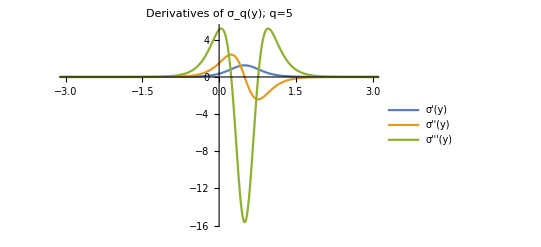

```mathematica
Table[D[σ[5,y],{y,k}],{k,1,3}]//FullSimplify
Plot[%,{y,-5,5},PlotLegends->{"σ'(y)","σ''(y)","σ'''(y)"},PlotRange->{{-3,3},All},PlotLabel->"Derivatives of σ_q(y); q=5"]
```

```mathematica
(* EXAMPLES *)
```

```mathematica
(* N=3, smooth *)
```

```mathematica
(* compute and plot the preference functions *)
```

```mathematica
p[t]={t,1-t,1/2(1+Cos[2 π t])};
n=Length[p[t]];
```

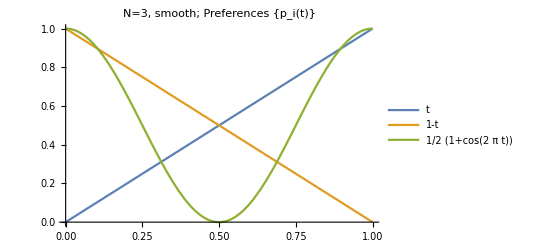

```mathematica
Plot[{t,1-t,1/2(1+Cos[2 π t])},{t,0,1},PlotLegends->"Expressions",PlotLabel->"N=3, smooth; Preferences {p_i(t)}"]
```

```mathematica
ParametricPlot3D[{t,1-t,Cos[2 π t]},{t,0,1},PlotLabel->"Group Preference {p_i(t)}"]
```

-Graphics3D-

```mathematica
(* compute and plot total function *)
```

```mathematica
f[q_,t_]=(1/n)*Sum[σ[q,p[t][[i]]],{i,1,n}];
```

```mathematica
Manipulate[Plot[f[q,t],{t,0,1},PlotLabel->"N=3, smooth, f_q(t), q="<>ToString[q],PlotRange->{0,1}],{q,0,100,.1}]
```

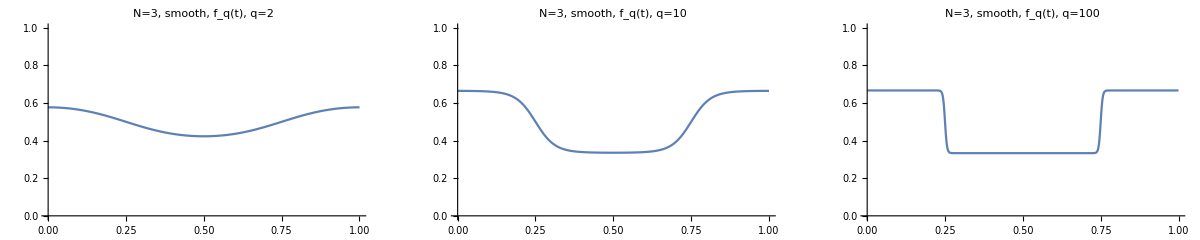

```mathematica
GraphicsRow[{Plot[f[2,t],{t,0,1},PlotLabel->"N=3, smooth, f_q(t), q=2",PlotRange->{0,1}],Plot[f[10,t],{t,0,1},PlotLabel->"N=3, smooth, f_q(t), q=10",PlotRange->{0,1}],Plot[f[100,t],{t,0,1},PlotLabel->"N=3, smooth, f_q(t), q=100",PlotRange->{0,1}]}]
```

```mathematica
(* compute and plot the derivative *)
```

```mathematica
df[q_,t_]=D[f[q,t],t];
```

```mathematica
Manipulate[Plot[df[q,t],{t,0,1},PlotLabel->"f'_q(t), q="<>ToString[q],PlotRange->All],{q,0,100,.1}]
```

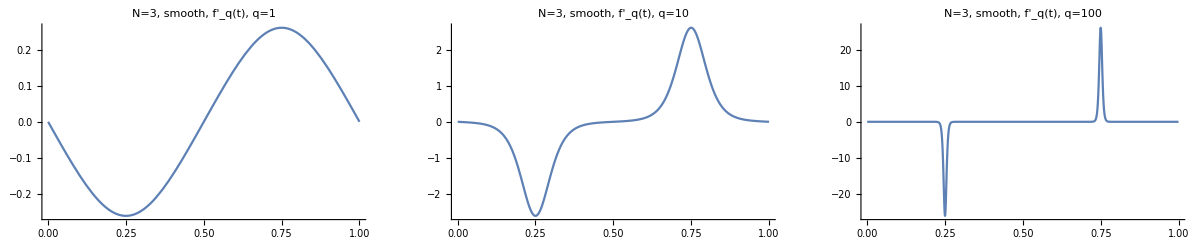

```mathematica
GraphicsRow[{Plot[df[1,t],{t,0,1},PlotLabel->"N=3, smooth, f'_q(t), q=1",PlotRange->All],Plot[df[10,t],{t,0,1},PlotLabel->"N=3, smooth, f'_q(t), q=10",PlotRange->All],Plot[df[100,t],{t,0,1},PlotLabel->"N=3, smooth, f'_q(t), q=100",PlotRange->All]}]
```

```mathematica
(* N=5, 100, 1000; random sinusoidals around y=1/2 *)
```

```mathematica
m=1000;
P[t]=Table[1/2+RandomReal[{0,.1}]*Cos[2*Pi*RandomReal[{-10,10}]*t+10*RandomReal[{-10,10}]],{i,1,m}];
```

```mathematica
sS=SparseArray[Table[{i,S[[i]]}->1,{i,1,Length[S]}],{10001,1000}];
```

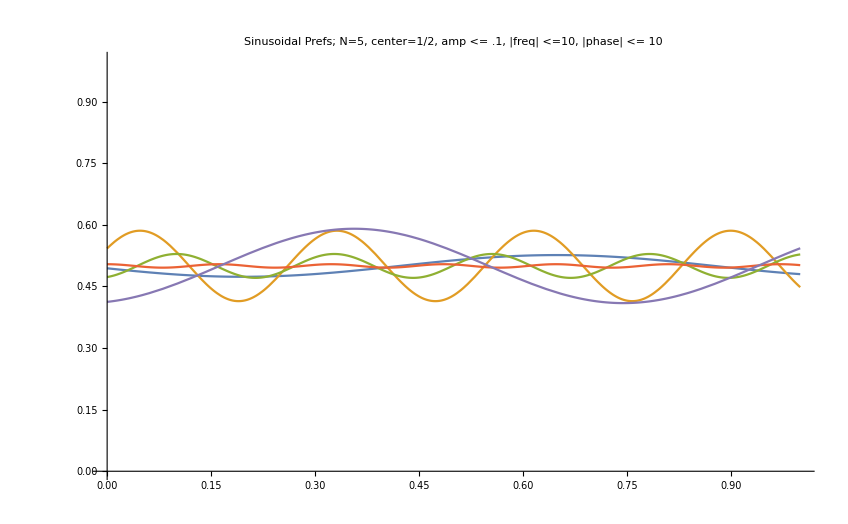

```mathematica
Plot[P[t],{t,0,1},PlotRange->{0,1},PlotLabel->"Sinusoidal Prefs; N="<>ToString[m]<>", center=1/2, amp <= .1, |freq| <=10, |phase| <= 10"]
```

```mathematica
F[q_,t_]=(1/m)*Sum[σ[q,P[t][[i]]],{i,1,m}];
```

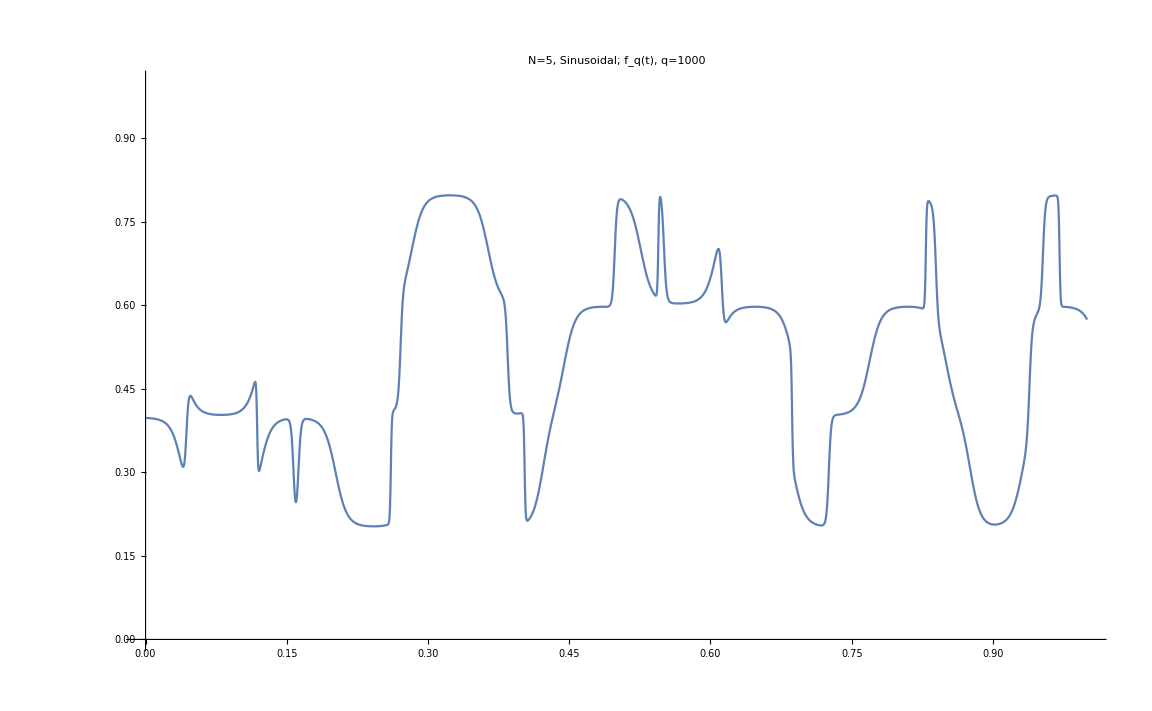

```mathematica
Plot[F[1000,t],{t,0,1},PlotRange->{0,1},PlotLabel->"N=" <>ToString[m]<>", Sinusoidal; f_q(t), q=1000"]
```

```mathematica
Manipulate[Plot[F[q,t],{t,0,1},PlotRange->{0,1},PlotLabel->"f_q(t); q="<>ToString[q]],{q,0,1000}]
```

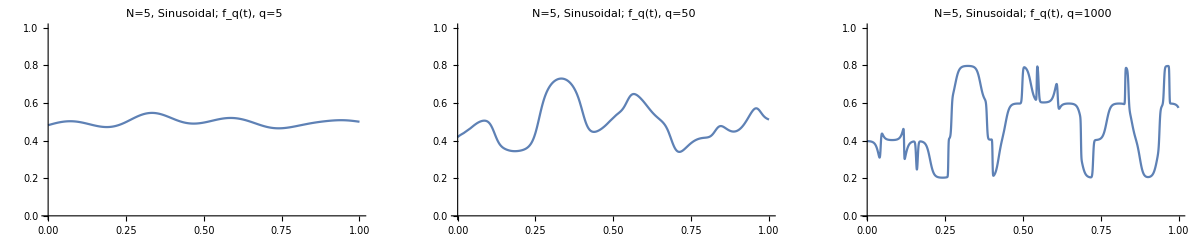

```mathematica
GraphicsRow[{Plot[F[5,t],{t,0,1},PlotRange->{0,1},PlotLabel->"N="<>ToString[m]<>", Sinusoidal; f_q(t), q=5"],Plot[F[50,t],{t,0,1},PlotRange->{0,1},PlotLabel->"N="<>ToString[m]<>", Sinusoidal; f_q(t), q=50"],Plot[F[1000,t],{t,0,1},PlotRange->{0,1},PlotLabel->"N="<>ToString[m]<>", Sinusoidal; f_q(t), q=1000"]}]
```

```mathematica
(* compute and plot the derivative *)
```

```mathematica
dF[q_,t_]=D[F[q,t],{t,1}];
```

```mathematica
Manipulate[Plot[dF[q,t],{t,0,1},PlotRange->All,PlotLabel->"N="<>ToString[m]<>", Sinusoidal; f'_q(t), q="<>ToString[q]],{q,0,1000}]
```

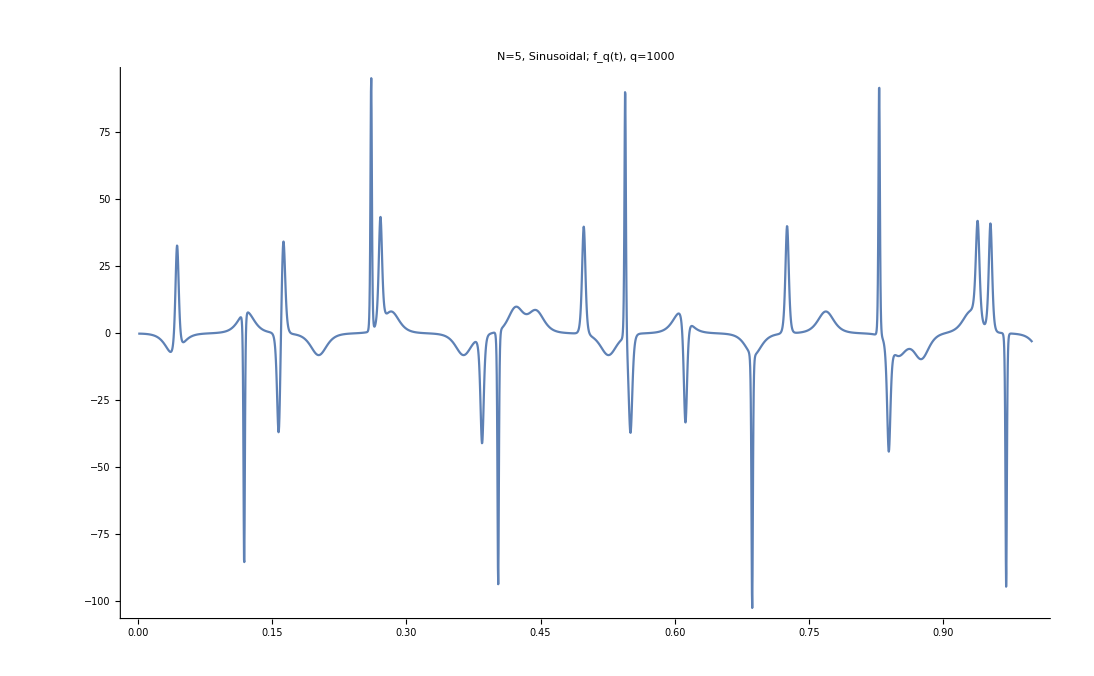

```mathematica
Plot[dF[1000,t],{t,0,1},PlotRange->All,PlotLabel->"N=" <>ToString[m]<>", Sinusoidal; f_q(t), q=1000"]
```

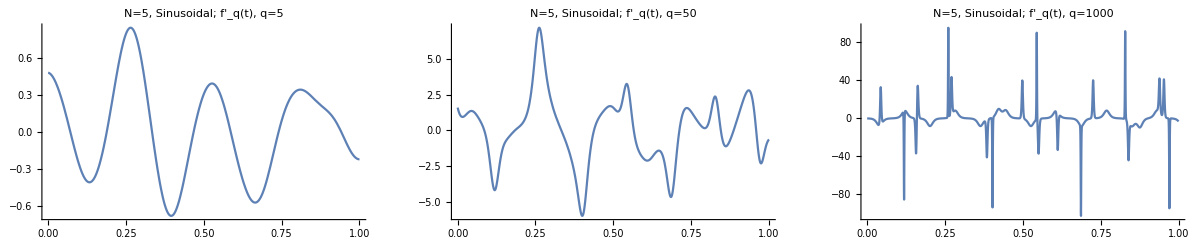

```mathematica
GraphicsRow[{Plot[dF[5,t],{t,0,1},PlotRange->All,PlotLabel->"N="<>ToString[m]<>", Sinusoidal; f'_q(t), q=5"],Plot[dF[50,t],{t,0,1},PlotRange->All,PlotLabel->"N="<>ToString[m]<>", Sinusoidal; f'_q(t), q=50"],Plot[dF[1000,t],{t,0,1},PlotRange->All,PlotLabel->"N="<>ToString[m]<>", Sinusoidal; f'_q(t), q=1000"]}]
```

```mathematica
(* N=3 cont. piecewise linear example *)
```

```mathematica
(* define the preference functions *)
```

```mathematica
p3[t_]=Piecewise[{{t,0≤t≤1/3},{1/3,1/3<t≤2/3},{2t-1,2/3<t≤1}}];
```

```mathematica
P2[t]={t,1-t,p3[t]};
l=Length[P2[t]];
```

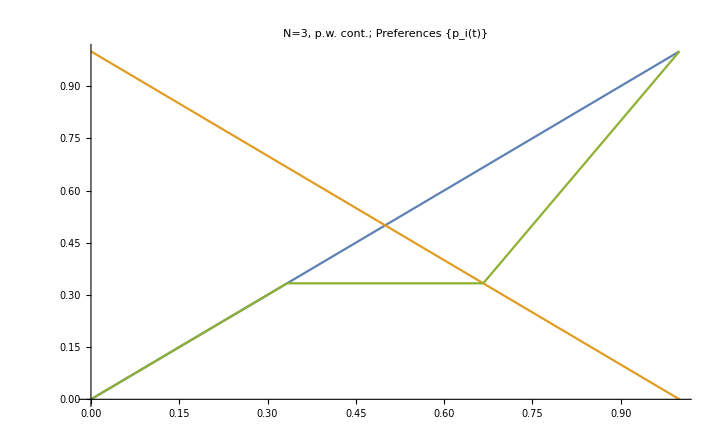

```mathematica
Plot[P2[t],{t,0,1},PlotLabel->"N=3, p.w. cont.; Preferences {p_i(t)}"]
```

```mathematica
(* compute the total function *)
```

```mathematica
H[q_,t_]=(1/l)*Sum[σ[q,P2[t][[i]]],{i,1,l}];
```

```mathematica
Manipulate[Plot[H[q,t],{t,0,1},PlotRange->{0,1},PlotLabel->"N=3, pw cont., f_q(t),q="<>ToString[q]],{q,0,1000,.1}]
```

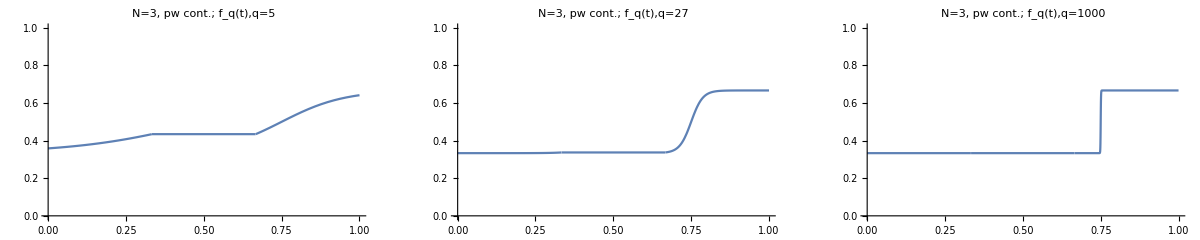

```mathematica
GraphicsRow[{Plot[H[5,t],{t,0,1},PlotRange->{0,1},PlotLabel->"N=3, pw cont.; f_q(t),q=5"],Plot[H[27,t],{t,0,1},PlotRange->{0,1},PlotLabel->"N=3, pw cont.; f_q(t),q=27"],Plot[H[1000,t],{t,0,1},PlotRange->{0,1},PlotLabel->"N=3, pw cont.; f_q(t),q=1000"]}]
```

```mathematica
(* compute and plot the derivative *)
```

```mathematica
dH[q_,t_]=FullSimplify[D[H[q,t],t]]
```

Piecewise[{{1/12 q Sech[1/4 (q-2 q t)]^2, 0<t<1/3}, {1/6 q Sech[q (3/4-t)]^2, 2/3<t<1}, {0, 1/3<t<2/3||t>1||t<0}, {Indeterminate, True}}]

```mathematica
Manipulate[Plot[dH[q,t],{t,0,1},PlotRange->{{0,1},All},PlotLabel->"N=3, pw cont.; f'_q(t),q="<>ToString[q]],{q,0,1000,.1}]
```

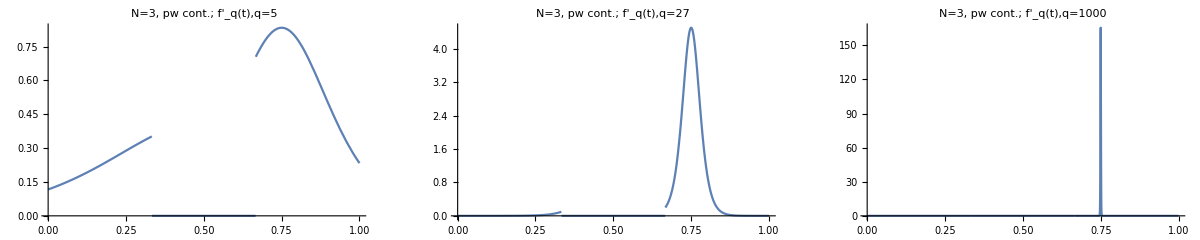

```mathematica
GraphicsRow[{Plot[dH[5,t],{t,0,1},PlotRange->{{0,1},All},PlotLabel->"N=3, pw cont.; f'_q(t),q=5"],Plot[dH[27,t],{t,0,1},PlotRange->{{0,1},All},PlotLabel->"N=3, pw cont.; f'_q(t),q=27"],Plot[dH[1000,t],{t,0,1},PlotRange->{{0,1},All},PlotLabel->"N=3, pw cont.; f'_q(t),q=1000"]}]
```